```mathematica
data=Import["eil51.tsp","Table"]
```

{{NAME,:,eil51},{COMMENT,:,51-city,problem,(Christofides/Eilon)},{TYPE,:,TSP},{DIMENSION,:,51},{EDGE_WEIGHT_TYPE,:,EUC_2D},{NODE_COORD_SECTION},{1,37,52},{2,49,49},{3,52,64},{4,20,26},{5,40,30},{6,21,47},{7,17,63},{8,31,62},{9,52,33},{10,51,21},{11,42,41},{12,31,32},{13,5,25},{14,12,42},{15,36,16},{16,52,41},{17,27,23},{18,17,33},{19,13,13},{20,57,58},{21,62,42},{22,42,57},{23,16,57},{24,8,52},{25,7,38},{26,27,68},{27,30,48},{28,43,67},{29,58,48},{30,58,27},{31,37,69},{32,38,46},{33,46,10},{34,61,33},{35,62,63},{36,63,69},{37,32,22},{38,45,35},{39,59,15},{40,5,6},{41,10,17},{42,21,10},{43,5,64},{44,30,15},{45,39,10},{46,32,39},{47,25,32},{48,25,55},{49,48,28},{50,56,37},{51,30,40},{EOF}}

```mathematica
pts=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]]
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
pts=Drop[Drop[data,6],-1][[All,2;;3]]
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

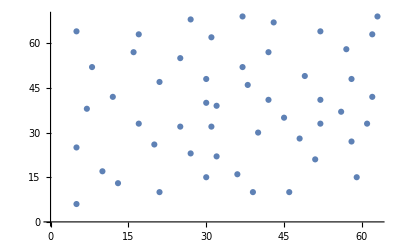

```mathematica
ListPlot[pts]
```

```mathematica
FindShortestTour[pts,PerformanceGoal->"Speed"]//N
```

{428.982,{1.,32.,11.,38.,5.,49.,10.,39.,33.,45.,15.,37.,17.,44.,42.,19.,40.,41.,13.,25.,14.,18.,4.,47.,12.,46.,51.,27.,6.,48.,23.,24.,43.,7.,26.,8.,31.,28.,3.,36.,35.,20.,29.,21.,34.,30.,9.,50.,16.,2.,22.,1.}}

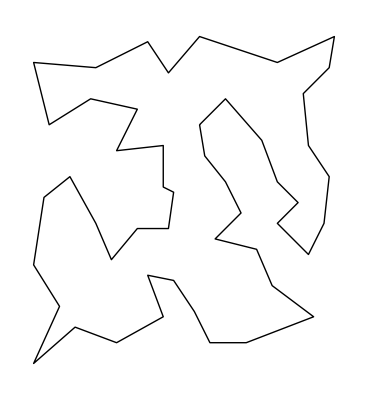

```mathematica
Graphics[Line[pts[[{1,32,11,38,5,49,10,39,33,45,15,37,17,44,42,19,40,41,13,25,14,18,4,47,12,46,51,27,6,48,23,24,43,7,26,8,31,28,3,36,35,20,29,21,34,30,9,50,16,2,22,1}]]]]
```

```mathematica
data=RandomInteger[100,{1000,2}];
```

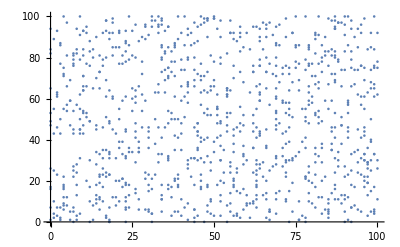

```mathematica
ListPlot[data]
```

```mathematica
FindShortestTour[data]
```

{675+322 √2+221 √5+100 √10+46 √13+34 √17+5 √26+7 √29+2 √34+2 √37+√41+√53+√65,{1,982,499,313,441,964,584,18,341,979,917,834,726,91,322,831,632,944,915,51,505,162,939,358,417,23,171,459,647,680,133,392,317,501,234,266,674,435,683,743,814,738,481,75,923,24,59,483,765,16,920,953,795,746,951,654,84,869,756,734,375,127,218,32,407,796,763,760,529,737,792,415,274,747,817,859,914,462,498,268,699,169,778,757,454,625,215,124,500,969,686,237,53,571,327,803,76,187,836,991,774,932,935,565,993,818,706,214,652,610,221,816,205,719,117,286,148,826,846,36,418,643,568,882,870,705,79,283,5,463,81,256,739,587,17,30,516,622,578,653,536,724,695,478,681,189,588,864,676,136,532,513,141,424,292,125,876,497,862,703,428,952,431,874,822,279,880,673,115,946,972,837,355,700,426,531,211,278,65,164,38,34,273,325,580,198,161,672,486,432,248,592,887,63,621,697,865,353,185,789,750,801,158,618,236,56,464,723,733,671,506,264,239,285,367,492,574,458,191,128,202,558,109,326,989,949,319,694,440,260,209,144,448,245,31,412,2,958,258,118,934,259,238,856,433,600,773,196,782,520,445,956,937,177,282,860,905,366,668,821,385,685,345,581,692,181,638,689,494,727,50,541,112,855,330,362,809,277,9,813,741,151,906,90,157,910,297,780,338,567,96,708,702,99,430,919,443,729,502,631,104,957,508,662,455,522,768,827,542,775,309,105,429,509,990,57,472,807,521,447,597,302,294,131,332,943,370,233,693,554,966,275,467,193,534,336,800,299,62,942,399,962,539,110,1000,845,572,403,469,675,970,776,749,710,173,514,557,725,404,263,310,772,363,470,295,892,848,493,519,512,938,434,931,948,471,947,168,576,628,988,930,712,924,153,103,89,489,730,456,549,709,998,736,43,936,986,933,761,401,921,192,216,410,540,491,154,223,987,194,308,414,422,788,69,241,116,925,835,781,555,854,408,547,890,178,526,139,922,669,771,616,61,252,296,977,928,764,552,748,550,711,684,641,280,231,395,728,664,533,504,473,640,852,629,635,376,907,575,240,758,766,767,360,487,787,58,527,67,197,255,113,866,368,208,200,537,589,900,960,573,68,667,593,339,994,71,762,190,306,41,468,270,135,677,8,929,213,783,785,15,314,374,696,224,320,394,973,95,518,627,229,199,528,720,838,55,940,108,7,851,523,321,687,212,156,402,460,222,45,582,20,382,679,420,754,49,678,777,195,636,844,204,106,978,732,249,312,690,446,634,400,873,242,457,160,670,46,840,744,388,698,281,288,784,155,996,976,243,798,4,272,560,453,261,379,599,228,642,707,594,811,247,721,551,86,201,815,963,875,337,72,546,163,633,926,918,913,897,438,298,387,150,419,927,878,819,174,877,799,657,770,714,372,617,26,405,329,626,902,364,396,590,841,656,271,909,19,300,480,179,452,22,556,579,607,140,97,889,142,54,427,615,849,265,893,548,436,254,3,896,474,477,586,825,833,891,373,585,175,713,101,324,912,70,688,170,888,371,868,591,828,665,691,126,423,28,146,916,184,406,595,235,602,85,496,666,451,639,553,804,102,461,752,210,881,623,745,450,624,850,318,351,716,369,959,354,29,42,984,630,342,644,475,899,975,983,566,858,381,47,735,663,769,391,903,230,253,307,83,78,791,269,812,786,303,608,413,701,731,176,207,605,132,759,715,121,601,180,77,722,482,227,619,217,361,206,225,503,172,950,941,359,349,21,884,357,895,879,530,416,333,805,100,559,904,10,437,138,779,267,646,603,39,842,244,48,348,611,293,961,853,562,250,262,997,165,425,289,583,411,808,794,476,27,74,543,383,484,661,94,755,182,147,393,985,645,609,861,871,246,655,444,25,152,220,479,954,287,965,525,183,82,563,538,751,316,524,830,847,11,823,390,820,561,604,829,564,304,843,149,378,544,790,999,857,955,945,365,40,510,356,659,488,232,87,311,449,6,389,901,810,614,350,995,119,352,535,251,507,867,44,73,328,740,159,648,980,908,598,971,397,226,384,143,839,802,742,651,377,465,886,346,335,305,137,166,682,832,442,290,114,545,495,257,344,824,992,704,122,872,52,717,797,409,466,33,120,64,577,894,658,331,649,111,863,515,620,276,301,380,490,613,968,37,167,596,650,12,883,753,981,80,718,511,129,439,323,123,98,284,35,517,398,347,188,134,60,14,66,130,340,885,793,485,186,898,315,88,386,334,570,606,92,569,343,145,974,291,637,911,612,107,13,203,806,967,219,660,93,421,1}}

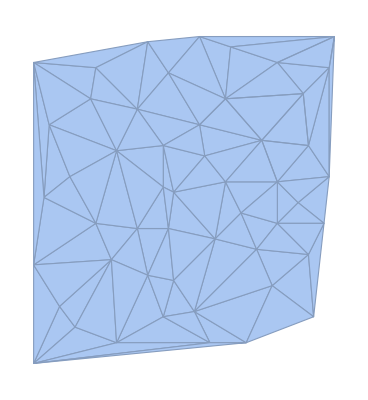

```mathematica
DelaunayMesh[pts]
```